# Quasi-Newton Updates

The idea behind Quasi-Newton updates is to approximate the Hessian (second derivative) using information from changes in the gradient (first derivative).  This is information that we are already evaluating.  As we will see the update equations (called the Secant Condition) give n equations (one vectors worth) in the n(n-1)/2 entries of a symmetric approximation to a Hessian.

We are stepping from x_k to x_(k+1).  
The step s_k=x_(k+1)-x_k,

We have the gradient ∇f_k=∇f(x_k) and compute the new gradient ∇f_(k+1)=∇f(x_(k+1)).  
The change in gradient is y_k=∇f_(k+1)-∇f_k.

If f=0.5x.B_(k+1).x+∇f_0.x+f_0 then ∇f(x)=B.x+∇f_0 and we should have
	∇f_k | = | B.x_k | + | ∇f_0
∇f_(k+1) | = | B.x_(k+1) |  + |  ∇f_0
Subtracting gives the Second Condition
	B_(k+1)(x_(k+1)-x_k) | = | ∇f_(k+1)-∇f_k
or equivalently
(Sec)	B_(k+1)s_k | = | y_k.

The symmetric n×n matrix B_(k+1) has n(n-1)/2 or roughly 0.5 n^2 entries. The Secant Condition is n linear equations. The Secant condition does not determine the new approximation B_(k+1).  There are lots of Quasi-Newton update schemes!

### SR1

The algebraically simplest is called SR1.  SR1 stands for Symmetric Rank One and updates an olde estimate B_k with a rank one matrix constructed from a single vector w.  In other words, 
	B_(k+1)=B_k+w⊗w
The advantages are that w is uniquely determined from s_k andy_k and the approximation can approximate non SPD Hessians.  The disadvantages are that there is no way to enforce a positive definite update and the update could well be large.

### SR1

The algebraically simplest is called SR1.  SR1 stands for Symmetric Rank One and updates an olde estimate B_k with a rank one matrix constructed from a single vector w.  In other words, 
	B_(k+1)=B_k+w⊗w
The advantages are that w is uniquely determined from s_k andy_k and the approximation can approximate non SPD Hessians.  The disadvantages are that the update could well be very large and there is no way to enforce a positive definite update.

The derivation for w is pretty simple. We will do it on the board.   The result is
	 B_(k+1)=B_k+((y_k-B_k s_k)⊗(y_k-B_k s_k))/((y_k-B_k s_k).s_k)
There is an equivalent update for H_k=B_k^-1 which is 
	 H_(k+1)=H_k+((s_k-H_k y_k)⊗(s_k-H_k y_k))/((s_k-H_k y_k).y_k)
You can derive the inverse formula just like the original or use the Sherman Morrison formula.

https://en.wikipedia.org/wiki/Sherman%E2%80%93Morrison_formula

https://en.wikipedia.org/wiki/Symmetric_rank-one

### BFGS and DFP

The most common update (default in most software) is BFGS.  The original Quasi-Newton update is DFP.  Both are algebraically clean rank two updates.  Both were motivated by scale invariance arguments. Both have justifications as minimizing the change from B_k
BFGS:	B_(k+1) | = | B_k | + | (y_k⊗y_k)/(y_k.s_k) | - | ((B_k s_k)⊗(B_k s_k))/(s_k.(B_k s_k)) 
DFP:    	B_(k+1)=(I-ρ_k y_k⊗s_k)B_k(I-ρ_k y_k⊗s_k)ᵀ+ρ_k y_k⊗y_k
with ρ_k=1/y_k.s_k.

You also frequently see update formulas for H_k=(B_k)^-1.  It is not an accident that these look like flipped around
BFGS:	H_(k+1) | = | (I-ρ_k s_k⊗y_k)H_k(I-ρ_k s_k⊗y_k)+ρ_k y_k⊗y_k 
DFP:    	H_(k+1)=H_k | + | (s_k⊗s_k)/(y_k.s_k) | - | ((H_k y_k)⊗(H_k y_k))/(y_k.(H_k y_k)) 
with ρ_k as before. The H versions come from the Sherman Morrison formula.  In specific and relevant ways these are minimal change formulas.

https://en.wikipedia.org/wiki/Broyden%E2%80%93Fletcher%E2%80%93Goldfarb%E2%80%93Shanno_algorithm

https://en.wikipedia.org/wiki/Davidon%E2%80%93Fletcher%E2%80%93Powell_formula

## Checking

```mathematica
SR1BUpdate[B_,{s_,y_}]:=Module[{r=y-B.s},B+ KroneckerProduct[r, r]/(r.s)]
SR1HUpdate[H_,{s_,y_}]:=SR1BUpdate[H,{y,s}]
```

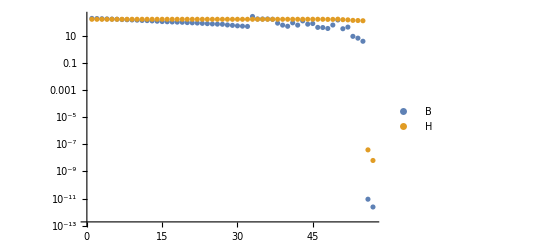

```mathematica
n=56; g=RandomReal[{-1,1}];
B0=RandomReal[{-1,1},{n,n}];B0=B0.B0ᵀ;
H0=Inverse[B0];
df[x_]:=B0.x+g
B=H=IdentityMatrix[n];
SR1Data=Table[
{x0,x1}=RandomReal[{-1,1},{2,n}];
s0=x1-x0;y0=df[x1]-df[x0];
B=SR1BUpdate[B,{s0,y0}];
H=SR1HUpdate[H,{s0,y0}];
{Norm[B-B0,"Frobenius"],Norm[H-H0,"Frobenius"]},
{n+1}]ᵀ;
ListLogPlot[
SR1Data,
PlotRange->All,
PlotLegends->{"B","H"}]
```

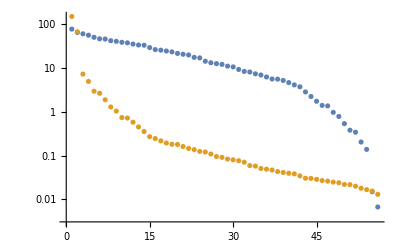

```mathematica
ListLogPlot[{
Eigenvalues[B0],
Abs[Eigenvalues[H0]]
}]
```

## Performance and Behavior